## Functions

```mathematica
Needs["Units`"];Needs["PhysicalConstants`"];
```

```mathematica
ρc=Convert[(3 (100Kilo Meter/Second/(Mega Parsec))^2)/(8π GravitationalConstant)SpeedOfLight^2,Joule/Meter^3]
```

(1.68815×10^-9 Joule)/Meter^3

```mathematica
h=.7;
```

```mathematica
ωγ=Convert[4StefanConstant/SpeedOfLight (2.72 Kelvin)^4/ρc,1]
```

0.0000245311

```mathematica
ωm=.27 h^2;
```

```mathematica
ργ[a_]:=If[a<4.6 10^-10,((4/11)^(4/3)),1]ωγ a^-4
```

```mathematica
ρm[a_,Neff_]:=ωm rfac[Neff]/rfac[3] a^-3
```

```mathematica
ρΛ[Neff_,mev_]:=h^2-ργ[1]-ρm[1,Neff]-ρνn[1,mev,Neff]
```

```mathematica
ρν[a_,m_]:=NIntegrate[(p^2 √(p^2+m^2))/(Exp[√((p a)^2+m^2)]-1),{p,0,∞}]
```

```mathematica
ρνn[a_,mev_,Neff_]:=Module[{a0,m},
a0=10^-4;
m=mev / Convert[2.72/a0 Kelvin*BoltzmannConstant/ElectronVolt,1];
Neff 7/8(4/11)^(4/3) ργ[a0]ρν[a/a0,m]/ρν[1,m]
]
```

```mathematica
rfac[Neff_]:=1+7/8 (4/11)^(4/3)Neff
```

## Legend

```mathematica
MyLegend[grid_,frame_:None]:=
Grid[grid/.x_?(MemberQ[{RGBColor,GrayLevel},Head[#]]&)->Show[Graphics[{x,Thickness[.05],Line[{{-5,0},{5,0}}]}],ImageSize->{50,10}],Frame->frame,Alignment->{Left,Center}]
```

```mathematica
addlegend[x_]:=Show[x,Epilog->Inset[Style[MyLegend[{{Darker[Blue], "Neutrinos"}, {Purple, "Photons"}, {Darker[Yellow], "Matter"}, {Darker[Green], "Dark Energy"}}],18],Log[{10^-7,.03}]]]
```

```mathematica
Style[MyLegend[{{Darker[Blue], "Neutrinos"}, {Purple, "Photons"}, {Darker[Yellow], "Matter"}, {Darker[Green], "Dark Energy"}}],18]
```

-Graphics- | Neutrinos
-Graphics- | Photons
-Graphics- | Matter
-Graphics- | Dark Energy

## Plot

```mathematica
makeplot[mev_,Neff_]:=LogLogPlot[Evaluate[a^4{ρνn[a,mev,Neff],ργ[a],ρm[a,Neff],ρΛ[Neff,mev]}],{a,10^-11,1},Frame->True,PlotRange->{10^-6,1},FrameStyle->Thickness[Medium],LabelStyle->16,PlotStyle->Thick,ImageSize->500,FrameLabel->{"TraditionalForm`a - scale factor","Ω_xh^2a^4"}]//Quiet
```

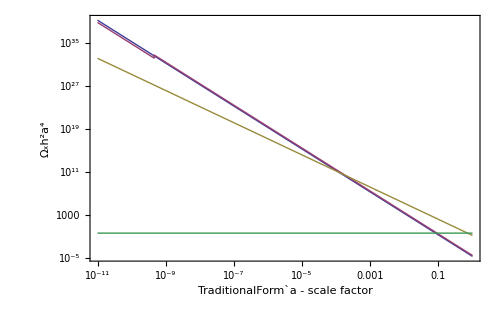

```mathematica
LogLogPlot[Evaluate[{ρνn[a,0,3],ργ[a],ρm[a,3],ρΛ[3,0]}],{a,10^-11,1},Frame->True,FrameStyle->Thickness[Medium],LabelStyle->16,PlotStyle->Thick,ImageSize->500,FrameLabel->{"TraditionalForm`a - scale factor","Ω_xh^2a^4"}]//Quiet
```

### 1

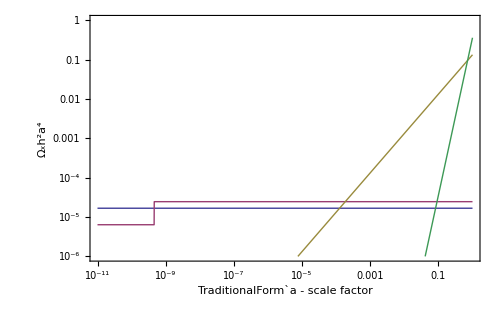

```mathematica
makeplot[0,3]
```

### 1 & 2

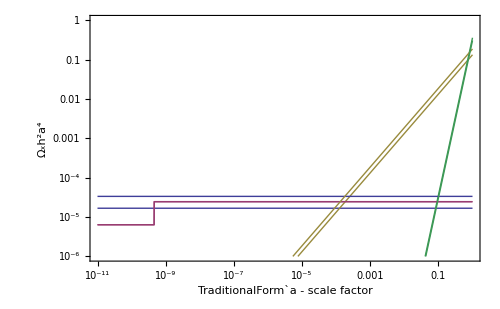

```mathematica
Show[{makeplot[0,3],makeplot[0,6]}]
```

### 1,3,4,5

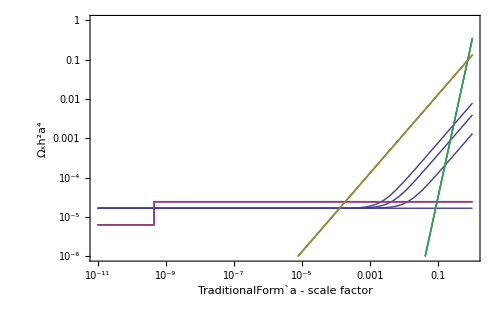

```mathematica
Show[{makeplot[0,3],makeplot[0.05,3],makeplot[0.15,3],makeplot[0.3,3]}]
```